```mathematica
<<Radia`
radUtiDelAll[]; (*Erase all previous elements*)
RadPlot3DOptions[];
```

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

## Parameters

```mathematica
(*========= Magnet design *)
(*DU52.5mm*)
espessurab=13;  (*Block Thickness*)
dist=0.125;  (*gap between blocks*)
gap=13.6;  (*Gap for chamber*)
magn=1.37;  (*magnetization of blocks*)
magnetization={magn,0.00};  (*magnetization of blocks / tolerance of magnetization*)
nperiods=21; periodL=(espessurab+dist)*4; (*number and size of periods*) 
layers=nperiods*4; (*number of block layers*)
nblocks=layers*4; (*n° of normal size blocks *)
nTblocks=nblocks+4*(4+3); (*n° total of Blocks*)

(*DU21mm*)
(*
espessurab=5.2;  (*Block Thickness*)
dist=0.05;  (*gap between blocks*)
gap=7;  (*Gap for chamber*)
magn=1.37;  (*magnetization of blocks*)
nperiods=84/4; periodL=(espessurab+dist)*4; (*number and size of periods*) 
layers=nperiods*4; (*number of block layers*)
*)

(*========= Computation Parameters *)
oversize=200; (* distance [mm] to add on both sides of the undulator length, for calculations *)
ex=0; ey=0; (*Assembling errors*)

(*Field Calculation*)
ny=1000; nx=2000;
 xo=-oversize; xf=(nperiods+2)*periodL+oversize;

(*Forces*)
subdiv={2,4,4};(*{2,4,4};*)
subdivcass={1,1,1}; (*{2,2,2}*)

(*multipole error*)
yo=-6;yf=6;zo=-6;zf=6; ney=500;
```

## Functions

```mathematica
(*nb1=NotebookOpen["C:/Pedro/RADIA/Undulator_Functions.nb"];
SelectionMove[nb1,All,Notebook];
SelectionEvaluate[nb1]
(*NotebookClose[nb1]*)*)
```

## GenMag

```mathematica
(*==================================================
A partir de um valor de magnetização de referência, erro percentual de magnetização e um input pedindo a inclusão de erros nos blocos, gera uma lista de magnetizações para os blocos com erros aleatórios aplicados. A lista é gerada na ordem de montagem dos blocos (em espiral, passando pelos quatro blocos de cada layer em sequência, layer por layer)
==================================================*)

genMag[magnetization_]:=(
Module[{magn,periodMag,i,mag},
magn=magnetization[[1]];

(*Perfect Magnetization*)
periodMag={{0,0,magn},{0,0,magn},{0,0,-magn},{0,0,-magn},{-magn,0,0},{-magn,0,0},{magn,0,0},{magn,0,0},{0,0,-magn},{0,0,-magn},{0,0,magn},{0,0,magn},{magn,0,0},{magn,0,0},{-magn,0,0},{-magn,0,0}};

mag=Nest[Join[periodMag,#,1]&,periodMag,(nperiods-1)];

Return[mag]
];
)
```

## Draw

```mathematica
draw[mag_,magn_,ex_,ey_,checkgeo_,espessurab_,periodL_,dist_,layers_,gap_,mod_]:=(
Module[{i,j,block,error,thick,displacement},
block=Table[0,nblocks+4*(4+3)];
undulator=radObjCnt[{}]; 
modeslist={{0,0,0,0},{-1/4,0,-1/4,0},{-1/2,0,-1/2,0},{-1/4,0,1/4,0},{-1/4,-1/4,0,0},{-1/4,0,0,-1/4}}*periodL;
mode=modeslist[[mod]];

(*=========================== Reference Geometry *)
(*Geo A1, Delta 52.5,gap 13.6*)
If[checkgeo==1,
geo1={{-21.5,-56.8},{21.5,-56.8},{22.5,-55.8},{22.5,-48.6},{16.794,-44.454},{-16.794,-44.454},{-22.5,-48.6},{-22.5,-55.8}};
geo2= {{16.794,-44.454},{16.794,-40.746},{-16.794,-40.746},{-16.794,-44.454}};
geo3={{16.794,-40.746},{22.5,-36.6},{22.5,-26.1},{5.25,-6.8},{-5.25,-6.8},{-22.5,-26.1},{-22.5,-36.6},{-16.794,-40.746}};

adjust1=ConstantArray[{0,6.8-gap/2},Length[geo1]];
adjust2=ConstantArray[{0,6.8-gap/2},Length[geo2]];
adjust3=ConstantArray[{0,6.8-gap/2},Length[geo3]];

geo1=geo1+adjust1;geo2=geo2+adjust2;geo3=geo3+adjust3;

];

(*Geo A1, Delta 22,gap 7*)
If[checkgeo==2,
geo1={{-10.75,-28.5},{10.75,-28.5},{11.25,-28.0},{11.25,-24.4},{8.397,-22.327},{-8.397,-22.327},{-11.25,-24.4},{-11.25,-28.0}};
geo2= {{8.397,-22.327},{8.397,-20.473},{-8.397,-20.473},{-8.397,-22.327}};
geo3={{8.397,-20.473},{11.25,-18.4},{11.25,-13.15},{2.625,-3.5},{-2.625,-3.5},{-11.25,-13.15},{-11.25,-18.4},{-8.397,-20.473}};

adjust1=ConstantArray[{0,3.5-gap/2},Length[geo1]];
adjust2=ConstantArray[{0,3.5-gap/2},Length[geo2]];
adjust3=ConstantArray[{0,3.5-gap/2},Length[geo3]];

geo1=geo1+adjust1;geo2=geo2+adjust2;geo3=geo3+adjust3;

];



(*=========================== Termination Front *)
thick={1/4,1/2,3/4,1}*espessurab; 
magTerm={{0,0,magn},{0,0,magn},{0,0,-magn},{0,0,-magn},{-magn,0,0},{-magn,0,0},{magn,0,0},{magn,0,0},{0,0,-magn},{0,0,-magn},{0,0,magn},{0,0,magn},{magn,0,0},{magn,0,0},{-magn,0,0},{-magn,0,0}};

For[j=1,j≤4,j++,
For[i=1,i≤4,i++,
(*Define Geometry*)
If[checkgeo==1 || checkgeo==2,
obj1=radObjThckPgn[(j-1)*0.875*(periodL/4),thick[[j]],geo1,magTerm[[(j-1)*4+i]]];
obj2=radObjThckPgn[(j-1)*0.875*(periodL/4),thick[[j]],geo2,magTerm[[(j-1)*4+i]]];
obj3=radObjThckPgn[(j-1)*0.875*(periodL/4),thick[[j]],geo3,magTerm[[(j-1)*4+i]]];

block[[(j-1)*4+i]]=radObjCnt[{obj1,obj2,obj3}];
];

(*Aplica Modo de Operação*)
displacement=radTrfTrsl[{mode[[i]],0,0}];
radTrfOrnt[block[[(j-1)*4+i]],displacement];
(*Aplica Rotação*)
radTrfOrnt[block[[(j-1)*4+i]],radTrfRot[{0,0,0},{1,0,0},(i-1)*Pi/2]];

(* Aplica Erros de Posição
erro=radTrfTrsl[{0,error[[4*(layers+i-1)+1,1]],error[[4*(layers+i-1)+1,2]]}];
radTrfOrnt[block[[1]],erro];*)

(*Apply Material and Magnetization*)
vacodym745ap=radMatLin[{0.04,0.04},magTerm[[(j-1)*4+i]]];
radMatApl[block[[(j-1)*4+i]],vacodym745ap]; 


radObjAddToCnt[undulator,{block[[(j-1)*4+i]]}];
];
];

(*=========================== Periods *)
For[j=1,j≤layers,j++,
For[i=1,i≤4,i++,
(*Define Geometry*)
If[checkgeo==1 || checkgeo==2,
obj1=radObjThckPgn[3.625*periodL/4+(j-1)*periodL/4,espessurab,geo1,mag[[(j-1)*4+i]]];
obj2=radObjThckPgn[3.625*periodL/4+(j-1)*periodL/4,espessurab,geo2,mag[[(j-1)*4+i]]];
obj3=radObjThckPgn[3.625*periodL/4+(j-1)*periodL/4,espessurab,geo3,mag[[(j-1)*4+i]]];

block[[(j-1+4)*4+i]]=radObjCnt[{obj1,obj2,obj3}];
];

(*Aplica Modo de Operação*)
displacement=radTrfTrsl[{mode[[i]],0,0}];
radTrfOrnt[block[[(j-1+4)*4+i]],displacement];
(*Aplica Rotação*)
radTrfOrnt[block[[(j-1+4)*4+i]],radTrfRot[{0,0,0},{1,0,0},(i-1)*Pi/2]];

(* Aplica Erros de Posição
erro=radTrfTrsl[{0,error[[4*(layers+i-1)+1,1]],error[[4*(layers+i-1)+1,2]]}];
radTrfOrnt[block[[1]],erro];*)

(*Apply Material and Magnetization*)
vacodym745ap=radMatLin[{0.04,0.04},mag[[(j-1)*4+i]]];
radMatApl[block[[(j-1+4)*4+i]],vacodym745ap]; 

radObjAddToCnt[undulator,{block[[(j-1+4)*4+i]]}];
];
];

(*=========================== Termination Back *)

For[j=1,j≤3,j++,
For[i=1,i≤4,i++,
(*Define Geometry*)
If[checkgeo==1 || checkgeo==2,
obj1=radObjThckPgn[(3.625+layers-1)*periodL/4+j*0.875*periodL/4,thick[[-(j+1)]],geo1,magTerm[[(j-1)*4+i]]];
obj2=radObjThckPgn[(3.625+layers-1)*periodL/4+j*0.875*periodL/4,thick[[-(j+1)]],geo2,magTerm[[(j-1)*4+i]]];
obj3=radObjThckPgn[(3.625+layers-1)*periodL/4+j*0.875*periodL/4,thick[[-(j+1)]],geo3,magTerm[[(j-1)*4+i]]];

block[[(j-1+layers+4)*4+i]]=radObjCnt[{obj1,obj2,obj3}];
];

(*Aplica Modo de Operação*)
displacement=radTrfTrsl[{mode[[i]],0,0}];
radTrfOrnt[block[[(j-1+layers+4)*4+i]],displacement];
(*Aplica Rotação*)
radTrfOrnt[block[[(j-1+layers+4)*4+i]],radTrfRot[{0,0,0},{1,0,0},(i-1)*Pi/2]];

(* Aplica Erros de Posição
erro=radTrfTrsl[{0,error[[4*(layers+i-1)+1,1]],error[[4*(layers+i-1)+1,2]]}];
radTrfOrnt[block[[1]],erro];*)

(*Apply Material and Magnetization*)
vacodym745ap=radMatLin[{0.04,0.04},magTerm[[(j-1)*4+i]]];
radMatApl[block[[(j-1+layers+4)*4+i]],vacodym745ap]; 

radObjAddToCnt[undulator,{block[[(j-1+layers+4)*4+i]]}];
];
];
(* Rotate undulator (Vale regra da mão direita) *)
radTrfOrnt[undulator,radTrfRot[{-10,0,0},{10,0,0},-Pi/4]];

(* Display Drawing *)
Print[Button["Plot Undulator",Print[Show[Graphics3D[radObjDrw[undulator],PlotLabel->"Delta Undulator 52.5",BaseStyle->{14,FontFamily->"Times"}],ImageMargins->5,ImageSize->{600,350}]]
]];

];

Return[undulator]
)
```

## Solve

```mathematica
solve[undulator_,magn_]:=(

t0=AbsoluteTime[];
(*=============== Material *)
vacodym745ap=radMatLin[{0.04,0.04},magn];  (*Susceptibility=Permeability-1*) 
radMatApl[undulator,vacodym745ap]; 

(*=============== Solve *)

abs=1*^-12; rel=abs; zero=abs;
radFldLenTol[abs,rel,zero];
radObjDivMag[undulator,{1,2,2}];

re=RadSolve[undulator,1*^-12,100000];

(*=============== Separate by Cassettes *)
cassetes=Table[{radObjCntStuf[undulator][[1+(i-1)*4]],radObjCntStuf[undulator][[2+(i-1)*4]],radObjCntStuf[undulator][[3+(i-1)*4]],radObjCntStuf[undulator][[4+(i-1)*4]]},{i,1,Floor[Length[radObjCntStuf[undulator]]/4]}];

cass1=radObjCnt[cassetes[[All,1]]];
cass2=radObjCnt[cassetes[[All,2]]];
cass3=radObjCnt[cassetes[[All,3]]];
cass4=radObjCnt[cassetes[[All,4]]];

t1=AbsoluteTime[];  deltat=t1-t0;
(*Print[Style[StringForm["> Undulator System Solved! (elapsed time: `` [s])",N[deltat]],Bold,FontSize->14]];*)
Print["> Undulator System Solved! (elapsed time: ", deltat, "[s])"]

)
```

## Field Calc

```mathematica
field[undulator_,xo_,xf_,nx_]:=(
dx=(xf-xo)/nx;
t0=AbsoluteTime[];

(*======== Axis Field Calc*)
baxis=Table[radFld[undulator,"b",{x,0,0}],{x,xo,xf-dx,dx}];
btotal=Sqrt[baxis[[All,1]]^2+baxis[[All,2]]^2+baxis[[All,3]]^2];

t1=AbsoluteTime[];deltat=t1-t0;
(*Print[Style[StringForm["> Fields Calc. Solved! (elapsed time: `` [s])",N[deltat]],FontSize->14]];*)
Print["> Fields Calc. Solved! (elapsed time: ",deltat ,"[s])"];

(*Axis Plot*)
axispoints=Table[xo+(n-1)*dx,{n,1,nx}];

p1=ListLinePlot[Table[{axispoints[[i]],baxis[[i,1]]},{i,1,nx}],PlotLabel->"Bx at Axis",PlotRange->All,ImageSize->{400,190}];
p2=ListLinePlot[Table[{axispoints[[i]],baxis[[i,2]]},{i,1,nx}],PlotLabel->"By at Axis",PlotRange->All,ImageSize->{400,190}];
p3=ListLinePlot[Table[{axispoints[[i]],baxis[[i,3]]},{i,1,nx}],PlotLabel->"Bz at Axis",PlotRange->All,ImageSize->{400,190}];

Print[GraphicsRow[{p1,p2,p3},Spacings->{0,10},ImageSize->{1000,250},AspectRatio->Full]];

)
```

## Block Forces

```mathematica
bforces[undulator_,subdiv_]:=(

t0=AbsoluteTime[];

forces=Table[radFldEnrFrc[RotateLeft[radObjCntStuf[undulator],i-1][[1]],radObjCnt[RotateLeft[radObjCntStuf[undulator],i-1][[2;;Length[radObjCntStuf[undulator]]]]],"",subdiv],{i,1,Length[radObjCntStuf[undulator]]}];

t1=AbsoluteTime[];deltat=t1-t0;
Print[Style[StringForm["> Block Forces Solved! (elapsed time: `` [s])",N[deltat]],Bold,FontSize->14]];

(* Forces Module *)
absforce=Table[Norm[forces[[i]]]*1.0,{i,1,Length[forces]}];

(* Create Table of Forces separeted by cassettes *);
expforces=Table[{forces[[1+(i-1)*4]],forces[[2+(i-1)*4]],forces[[3+(i-1)*4]],forces[[4+(i-1)*4]]},{i,1,Floor[Length[forces]/4]}];
(*Print[StringForm["\t\tForces: \n{Layers | Cassettes | Force Components}: ``",Dimensions[expforces]]];*)

p1=ListPlot[{expforces[[All,1,1]],expforces[[All,1,2]],expforces[[All,1,3]]},Joined->True,PlotLegends->{"Fx","Fy","Fz"},PlotLabel->"Forces on Blocks: Cassete 1",PlotRange->All,ImageSize->{400,190}];
p2=ListPlot[{expforces[[All,2,1]],expforces[[All,2,2]],expforces[[All,2,3]]},Joined->True,PlotLegends->{"Fx","Fy","Fz"},PlotLabel->"Forces on Blocks: Cassete 2",PlotRange->All,ImageSize->{400,190}];
p3=ListPlot[{expforces[[All,3,1]],expforces[[All,3,2]],expforces[[All,3,3]]},Joined->True,PlotLegends->{"Fx","Fy","Fz"},PlotLabel->"Forces on Blocks: Cassete 3",PlotRange->All,ImageSize->{400,190}];
p4=ListPlot[{expforces[[All,4,1]],expforces[[All,4,2]],expforces[[All,4,3]]},Joined->True,PlotLegends->{"Fx","Fy","Fz"},PlotLabel->"Forces on Blocks: Cassete 4",PlotRange->All,ImageSize->{400,190}];

GraphicsGrid[{{p1,p2},{p3,p4}},Spacings->{0,10},ImageSize->{1000,400},AspectRatio->Full]

)
```

## Cassettes Forces

```mathematica
cforces[cass1_,cass2_,cass3_,cass4_,subdivcass_]:=(
t0=AbsoluteTime[];

forcecass1=radFldEnrFrc[cass1,radObjCnt[{cass2,cass3,cass4}],"",subdivcass];
forcecass2=radFldEnrFrc[cass2,radObjCnt[{cass1,cass3,cass4}],"",subdivcass];
forcecass3=radFldEnrFrc[cass3,radObjCnt[{cass1,cass2,cass4}],"",subdivcass];
forcecass4=radFldEnrFrc[cass4,radObjCnt[{cass1,cass2,cass3}],"",subdivcass];

forcescass={{forcecass1},{forcecass2},{forcecass3},{forcecass4}};

t1=AbsoluteTime[];deltat=t1-t0;
Print[Style[StringForm["> Cassettes Forces Solved! (elapsed time: `` [s])",N[deltat]],Bold,FontSize->14]];

Print[StringForm["> Force on Cassette 1: \n\t``\n> Force on Cassette 2: \n\t``\n> Force on Cassette 3: \n\t``\n> Force on Cassette 4: \n\t`` \n",forcecass1,forcecass2,forcecass3,forcecass4]];

)
```

## Multipole Error

```mathematica
mpError[undulator_,gap_,yo_,yf_,ney_]:=(

dy=(yf-yo)/ney;

multipole=radObjCnt[radObjCntStuf[undulator][[17;;20]]];

t0=AbsoluteTime[];
remulti=RadSolve[multipole,1*^-10,1000];

(*===================== Error Calc*)
rref=2/3*gap; order=6;
(*Vertical*)
bplanev=Table[radFld[multipole,"b",{0,y,y}],{y,yo,yf,dy}];
(*Horiz*)
bplaneh=Table[radFld[multipole,"b",{0,y,-y}],{y,yo,yf,dy}];
bmultiv=Sqrt[bplanev[[All,2]]^2+bplanev[[All,3]]^2];
bmultih=Sqrt[bplaneh[[All,2]]^2+bplaneh[[All,3]]^2];

pointsv=Table[{yo+(n-1)*dy,bmultiv[[n]]},{n,1,ney}];
pointsh=Table[{yo+(n-1)*dy,bmultih[[n]]},{n,1,ney}];

(* B_ana = Bz+iBy *);
banalytv=bplanev[[All,3]]+I*bplanev[[All,2]]; 
banalyth=bplaneh[[All,3]]+I*bplaneh[[All,2]]; 

bmatrix = Join[banalytv,banalyth];

(*---Solve the Indeterminance: 0^0 *)
Unprotect[Power];
Power[0|0.,0|0.]=1;
Protect[Power];
(*---*)

(* pos = ((y+iz)/rref)^(order-1) *)
posv=Table[((y+I*y)/rref)^(i-1),{y,yo,yf,dy},{i,1,order}]; 
posh=Table[((y-I*y)/rref)^(i-1),{y,yo,yf,dy},{i,1,order}];
posmatrix=Join[posv,posh,1];

(*Solve the System: (y+iz). matrixZ = (Bz+iBy) *)
matrixZ=LeastSquares[posmatrix,bmatrix];  (*mx=b*)
matrixZ=matrixZ/Abs[Max[Abs[matrixZ]]];

t1=AbsoluteTime[];deltat=(t1-t0);
Print[Style[StringForm["> Multipole Error Solved! (elapsed time: `` [s])",N[deltat]],Bold,FontSize->14]];

(*===================== Plots*)
p1=ListPlot[pointsv,FrameLabel->{"Dist_Vertical [mm]","|B| [T]"},PlotLabel->"Vertical Axis Field",Frame->True,PlotRange->All,GridLines->Automatic,ImageSize->{300,190}];
p2=ListPlot[pointsh,FrameLabel->{"Dist_Horizontal [mm]","|B| [T]"},PlotLabel->"Horizontal Axis Field",Frame->True,PlotRange->All,GridLines->Automatic,ImageSize->{300,190}];
p3=ListPlot[Abs[matrixZ],Filling->Bottom,FillingStyle->Thickness[6*^-3],PlotStyle->{PointSize[0.02]},PlotMarkers->"OpenMarkers",PlotLabel-> "Multipole Harmonic Components",FrameLabel->{"Harmonic Component","Multipole Error"},Frame->True,GridLines->Automatic,PlotRange->{{0,6.5},{-2*^-2,1.1}},ImageSize->{300,190}];

Print[StringForm["\t Harmonic Components: `` \n", NumberForm[Abs[matrixZ],4]]];

Print[GraphicsRow[{p1,p2,p3},Spacings->Scaled[0.1],ImageSize->{1000,220}]];

)
```

## Integral Error

```mathematica
interror[undulator_,xo_,xf_,nx_]:=(
Module[{baxis,integralx01,integralx02,integraly01,integraly02,integralz01,integralz02,integralx1,integralx2,integraly1,integraly2,integralz1,integralz2},
dx=Abs[xf-xo]/nx;
baxis=Table[radFld[undulator,"b",{x,0,0}],{x,xo,xf-dx,dx}];

(*---X---*)
integralx01=Table[ (baxis[[i,1]]+baxis[[i+1,1]])/2*dx *10^-3,{i,1,Length[baxis]-1}]; (* [T.m] *)
integralx1=Accumulate[integralx01];
(*Print["(By) 1st Integral: ",integralx1[[Length[integralx1]]],"[T.m] = ",integralx1[[Length[integralx1]]]*1*^4*100,"[G.cm]"];*)

integralx02=Table[ (integralx1[[i]]+integralx1[[i+1]])/2*dx*10^-3 ,{i,1,Length[integralx1]-1}]; (* [T.m.b2] *)
integralx2=Accumulate[integralx02];
(*Print["(By) 2nd Integral: ",integralx2[[Length[integralx2]]]*10^4*100^2,"[G.m.b2]"];*)

(*---Y---*)
integraly01=Table[ (baxis[[i,2]]+baxis[[i+1,2]])/2*dx *10^-3,{i,1,Length[baxis]-1}]; (* [T.m] *)
integraly1=Accumulate[integraly01];
Print["(By) 1st Integral: ",integraly1[[Length[integraly1]]],"[T.m] = ",integraly1[[Length[integraly1]]]*1*^4*100,"[G.cm]"];

integraly02=Table[ (integraly1[[i]]+integraly1[[i+1]])/2*dx*10^-3 ,{i,1,Length[integraly1]-1}]; (* [T.m.b2] *)
integraly2=Accumulate[integraly02];
Print["(By) 2nd Integral: ",integraly2[[Length[integraly2]]]*10^4*100^2,"[G.cm.b2]"];

(*---Z---*)
integralz01=Table[ (baxis[[i,3]]+baxis[[i+1,3]])/2*dx *10^-3,{i,1,Length[baxis]-1}]; (* [T.m] *)
integralz1=Accumulate[integralz01];
Print["(Bz) 1st Integral: ",integralz1[[Length[integralz1]]],"[T.m] = ",integralz1[[Length[integralz1]]]*1*^4*100,"[G.cm]"];

integralz02=Table[ (integralz1[[i]]+integralz1[[i+1]])/2*dx*10^-3 ,{i,1,Length[integralz1]-1}]; (* [T.m] *)
integralz2=Accumulate[integralz02];
Print["(Bz) 2nd Integral: ",integralz2[[Length[integralz2]]]*10^4*100^2,"[G.cm.b2]"];


Return[{integralx1,integralx2,integraly1,integraly2,integralz1,integralz2}]
];
)
```

```mathematica
interror2[undulator_,xo_,xf_,np_]:=(
Module[{baxis,i,dx,area,area2,integral,int,int2},
re=RadSolve[undulator,1*^-12,100000];

(*------ Fisrt Integral*)
t0=AbsoluteTime[];
(*
integral=radFldInt[undulator,"fin","",{xo,0,0},{xf,0,0}];
integral=(integral*10^4)/10; (*Tesla.mm to Gauss.cm*)
*)
dx=(xf-xo)/np;
baxis=Table[radFld[undulator,"b",{x,0,0}],{x,xo,xf-dx,dx}];
area=Table[{(baxis[[i,1]]+baxis[[i+1,1]])/2*dx,(baxis[[i,2]]+baxis[[i+1,2]])/2*dx,(baxis[[i,3]]+baxis[[i+1,3]])/2*dx},{i,1,Length[baxis]-1}];
integral=Accumulate[area];

int= Sum[{area[[i,1]],area[[i,2]],area[[i,3]]},{i,1,Length[area]}];
int=(int*10^4)/10; 

(*-----Second Integral*)
area2=Table[{(integral[[i,1]]+integral[[i+1,1]])/2*dx,(integral[[i,2]]+integral[[i+1,2]])/2*dx,(integral[[i,3]]+integral[[i+1,3]])/2*dx},{i,1,Length[integral]-1}];

int2=Sum[{area2[[i,1]],area2[[i,2]],area2[[i,3]]},{i,1,Length[area2]}]*10^2; (*G.cm.b2*)

t1=AbsoluteTime[]; dt2=t1-t0;

Print["\n1st Integral [G.cm]: ", int,"\n2nd Integral [G.cm.b2]: ", int2]
];
)
```

## Phase Error

```mathematica
phaseerror[baxis_,btotal_,xo_,xf_,nx_]:=(
Module[{bfield,bfieldT,longAxis,s,ampX,ampY,ampZ,peakX,peakY,peakZ,peakT,longPeakX,longPeakY,longPeakZ,longPeakT,periods,nperiods,periodL,kparam,lambda,intField0,intField},
t0=AbsoluteTime[];
(*========= Physics Parameters =========*)
eletron=1.60217662*^-19; mo=9.10938356*^-31;
eRestEnergy=510998.92811; (*[eV]*) (* == mo*c^2[J]*)

bfield=baxis;
bfieldT=btotal;

(*Principal Longitudinal Axis*)
dx=(xf-xo)/nx;
longAxis=Table[xo+(n-1)*dx,{n,1,nx}];

(* Longitudinal Axis from 0 *)
s=(longAxis-longAxis[[1]])/1000;  (*[m]*)

(*========= Find Peaks =========*)
(*limits*)
ampX=0.1; ampY=0.1; ampZ=0.1;
(*Find Peaks*)
peakX=FindPeaks[bfield[[All,1]],0 ,0, ampX];
peakY=FindPeaks[bfield[[All,2]],0 ,0, ampY];
peakZ=FindPeaks[bfield[[All,3]],0 ,0, ampZ];
peakT=FindPeaks[bfieldT,0 ,0 , ampZ];

(* Remove extremities *)
drop=4; (*how many peaks to drop each side*)
peakT=Drop[peakT,{1,drop}];peakT=Drop[peakT,{-drop,-1}];
longPeakT=Table[s[[peakT[[i,1]]]],{i,1,Length[peakT]}];

drop=3; (*how many peaks to drop each side*)
If[Length[peakZ]>2*drop,
peakZ=Drop[peakZ,{1,drop}];peakZ=Drop[peakZ,{-drop,-1}];
longPeakZ=Table[longAxis[[peakZ[[i,1]]]],{i,1,Length[peakZ]}];
,
peakZ=ConstantArray[10^-5,{1,2}];
];

If[Length[peakY]>2*drop,
peakY=Drop[peakY,{1,drop}];peakY=Drop[peakY,{-drop,-1}];
longPeakY=Table[longAxis[[peakY[[i,1]]]],{i,1,Length[peakY]}];
,
peakY=ConstantArray[10^-5,{1,2}];
];

If[Length[peakX]>2*drop,
peakX=Drop[peakX,{1,drop}];peakX=Drop[peakX,{-drop,-1}];
longPeakX=Table[longAxis[[peakX[[i,1]]]],{i,1,Length[peakX]}];
,
peakX=ConstantArray[10^-5,{1,2}];
];

If[Mean[peakX[[All,2]]]>Mean[peakY[[All,2]]],
If[Mean[peakX[[All,2]]]>Mean[peakZ[[All,2]]],
longPeak=longPeakX;
,
longPeak=longPeakZ;
]
,
If[Mean[peakY[[All,2]]]>Mean[peakZ[[All,2]]],
longPeak=longPeakY;
,
longPeak=longPeakZ;
]
];

periods=Table[longPeak[[i+1]]-longPeak[[i]],{i,1,Length[longPeak]-1}];

(*========= Magnet design =========*)
nperiods=Length[periods];
periodL=Mean[periods]; (*mm*)
eEnergy=3*10^9; (*eV*)
gamma=eEnergy/eRestEnergy;
c=299792458; (*m/s*)
kparam=0.0934*periodL*Mean[peakT[[All,2]]];  (*!!!!!!!!!!!!! Todas componentes ou só 1? *)
lambda=((Mean[periods]/1000)/(2*(gamma^2)))*(1 + (kparam^2)/2); (*m*)
Print["\nK parameter: ",kparam,"\nWavelenght: ", lambda,"[m]"];

(*========= Integrals =========*)
intField0=Table[{(bfield[[i,1]]+bfield[[i+1,1]])/2*(longAxis[[i+1]]-longAxis[[i]])*10^-3,(bfield[[i,2]]+bfield[[i+1,2]])/2*(longAxis[[i+1]]-longAxis[[i]])*10^-3,(bfield[[i,3]]+bfield[[i+1,3]])/2*(longAxis[[i+1]]-longAxis[[i]])*10^-3},{i,1,Length[bfield]-1}]; (* [T.m] *)

intField={Accumulate[intField0[[All,1]]],Accumulate[intField0[[All,2]]],Accumulate[intField0[[All,3]]]};

(*========= Phase Function =========*)
I01[i_]:=(
Return[eletron/(gamma*mo*c)*intField[[1,i]]]
);

I03[i_]:=(
Return[eletron/(gamma*mo*c)*intField[[3,i]]]
);

I02[i_]:=(
Return[eletron/(gamma*mo*c)*intField[[2,i]]]
);

I2[j_]:=(
I0=Table[(((I01[i]^2+I01[i+1]^2)/2)+((I02[i]^2+I02[i+1]^2)/2)+((I03[i]^2+I03[i+1]^2)/2))*(s[[i+1]]-s[[i]]),{i,1,j}]; 
Return[Sum[I0[[i]],{i,1,Length[I0]}]];
);

(*========= Phase =========*)
phase=Table[Pi/lambda*(s[[j]]/gamma^2+I2[j]),{j,peakT[[1,1]],peakT[[Length[peakT],1]]-2}];

(*Phase Error*)
phaseError=Table[phase[[(peakT[[i+1,1]]-peakT[[1,1]]+1)]]-phase[[(peakT[[i,1]]-peakT[[1,1]]+1)]],{i,1,Length[peakT]-2}];
rmsError=RootMeanSquare[(phaseError-Pi)*180/Pi];
Print["(1) RMS Phase Error [deg]: ",rmsError];
(*Print[ListLinePlot[(phaseError-Pi)*180/Pi]];*)

(*========= Fitting ========= *)
fitData=Table[{s[[i]]+longPeakT[[1]],phase[[i]]},{i,1,Length[phase]}];
fitLin=NonlinearModelFit[fitData,a*x+b,{a,b},x];

linearFit=Table[{s[[i]]+longPeakT[[1]],fitLin[s[[i]]+longPeakT[[1]]]},{i,1,Length[phase]}];
linearizedPhase=phase-linearFit[[All,2]];

t1=AbsoluteTime[];
Print["\n> Phase Error solved! (elapsed time: ", t1-t0, "[s])"];

p3=ListLinePlot[linearizedPhase*180/Pi,PlotLabel->"Linearized Phase",ImageSize->{300,200},Frame->True,FrameLabel->{" ","[deg]"}];

errorP=Table[Mean[linearizedPhase[[peakT[[i,1]]-peakT[[1,1]]+1;;peakT[[i+1,1]]-peakT[[1,1]]-1]]],{i,1,Length[peakT]-1}]*180/Pi;
Print["(2-Fitting) RMS Phase Error [deg]: ",RootMeanSquare[errorP]];

Print[Row[{Show[p3],Show[ListLinePlot[errorP,ImageSize->{300,200},PlotMarkers->{Automatic, 5}]]}]]
];
)
```

## Save

```mathematica
save[i_,m_,expforces_,m0_,baxis_]:=(
If[i+1> 1,

If[MemberQ[check,2],
exportmatrix=Join[m,ArrayReshape[Flatten[expforces],{Length[expforces],12}],2]
];
If[MemberQ[check,1],
exportfield=Join[m0,baxis,2];
];
,
If[MemberQ[check,2],
exportmatrix=ArrayReshape[Flatten[expforces],{Length[expforces],12}]
];
If[MemberQ[check,1],
exportfield=baxis; ArrayReshape[Flatten[baxis],{Length[baxis],3}]
];

];

)
```

## Export

```mathematica
exportf[exportmatrix_,exportfield_]:=(
dir=NotebookDirectory[];

(*----Export*)
If[MemberQ[check,2],
(*Adjust Dimensions*)
d2=Dimensions[exportmatrix];
rest=48-d2[[2]];
exportmatrix2=Join[exportmatrix,ConstantArray[0,{Length[exportmatrix],rest}],2];
(*Export Field*)
Export[StringJoin[dir,"Forces_General_Modes.xlsx"],{"Fase_inicial"->exportmatrix2[[All,1;;12]],"Fase_Psobre2"->exportmatrix2[[All,13;;24]],"CF_Psobre4"->exportmatrix2[[All,25;;36]],"GV_Psobre4"->exportmatrix2[[All,37;;48]]}]
];

If[MemberQ[check,1],
(*Adjust Dimensions*)
d=Dimensions[exportfield];
rest=12-d[[2]];
exportfield2=Join[exportfield,ConstantArray[0,{Length[exportfield],rest}],2];
(*Export Field*)
Export[StringJoin[dir,"Field_General_Modes.xlsx"],{"Fase_inicial"->exportfield2[[All,1;;3]],"Fase_Psobre2"->exportfield2[[All,4;;6]],"CF_Psobre4"->exportfield2[[All,7;;9]],"GV_Psobre4"->exportfield2[[All,10;;12]]}]
];

)
```

## Execution

```mathematica
RadioButtonBar[Dynamic[checkgeo],{0-> "Delta 52.5mm: A0 Geometry",1-> "Delta 52.5mm: A1 Geometry",2-> "Delta 21mm"}]
CheckboxBar[Dynamic[check],{1-> "Field Calc.",2-> "Block Forces",3-> "Cassettes Forces",4->"Integral error",5->"Phase error"}]
CheckboxBar[Dynamic[checkmode],{1-> "Fase(0)",2-> "Fase(λ/2)",3-> "Contra-Fase(λ/4)",4->"GV(λ/4)"}]
CheckboxBar[Dynamic[checkexp],{1->"Export Results"}]
```

| Delta 52.5mm: A0 Geometry   | Delta 52.5mm: A1 Geometry   | Delta 21mm

| Field Calc.   | Block Forces   | Cassettes Forces   | Integral error   | Phase error

| Fase(0)   | Fase(λ/2)   | Contra-Fase(λ/4)   | GV(λ/4)

| Export Results

```mathematica
isave=0;
exportmatrix=0; exportfield=0;

mag=genMag[magnetization];
```

## Fase (Pol. Linear Horizontal)

Plot Undulator

> Undulator System Solved! (elapsed time: 27.580821[s])

> Fields Calc. Solved! (elapsed time: 9.9531242[s])

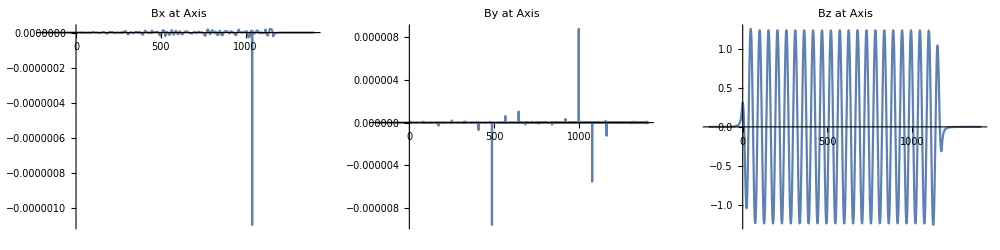

K parameter: 6.06294
Wavelenght: 1.47581×10^-8[m]

(1) RMS Phase Error [deg]: 1.70203

> Phase Error solved! (elapsed time: 26.782407[s])

(2-Fitting) RMS Phase Error [deg]: 0.447617

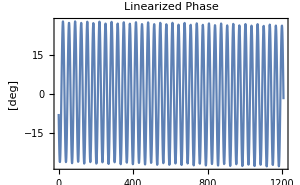
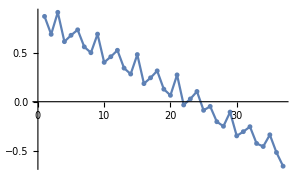

```mathematica
If[MemberQ[checkmode,1],

draw[mag,magn,ex,ey,checkgeo,espessurab,periodL,dist,layers,gap,1];
solve[undulator,magn];

If[MemberQ[check,1],field[undulator,xo,xf,nx]];
If[MemberQ[check,2],bforces[undulator,subdiv]];
If[MemberQ[check,3],cforces[cass1,cass2,cass3,cass4,subdivcass]];
If[MemberQ[check,4],interror[undulator,xo,xf,nx]];
If[MemberQ[check,4],interror2[undulator,xo,xf,nx]];
If[MemberQ[check,5],phaseerror[baxis,btotal,xo,xf,nx]];
If[MemberQ[check,6],mpError[undulator,gap,yo,yf,ney]];

save[isave,exportmatrix,expforces,exportfield,baxis]; isave=isave+1;

]
```

## Fase [lambda/2] (Pol. Linear Vertical)

Plot Undulator

> Undulator System Solved! (elapsed time: 31.32188[s])

> Fields Calc. Solved! (elapsed time: 9.937502[s])

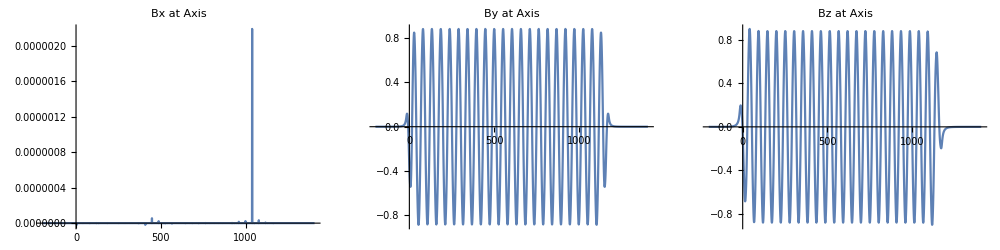

K parameter: 4.33373
Wavelenght: 7.91763×10^-9[m]

(1) RMS Phase Error [deg]: 11.9658

> Phase Error solved! (elapsed time: 27.329242[s])

(2-Fitting) RMS Phase Error [deg]: 0.680703

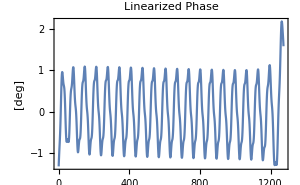
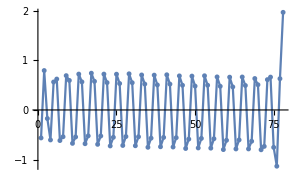

```mathematica
If[MemberQ[checkmode,2],

draw[mag,magn,ex,ey,checkgeo,espessurab,periodL,dist,layers,gap,2];

solve[undulator,magn];
If[MemberQ[check,1],field[undulator,xo,xf,nx]];
If[MemberQ[check,2],bforces[undulator,subdiv]];
If[MemberQ[check,3],cforces[cass1,cass2,cass3,cass4,subdivcass]];
If[MemberQ[check,4],interror2[undulator,xo,xf,nx]];
If[MemberQ[check,5],phaseerror[baxis,btotal,xo,xf,nx]];
If[MemberQ[check,6],mpError[undulator,gap,yo,yf,ney]];

save[isave,exportmatrix,expforces,exportfield,baxis];isave=isave+1;

]
```

## Contra-Fase [lambda/4] (Pol. Linear com Rot. 0-90.ba)

Plot Undulator

> Undulator System Solved! (elapsed time: 35.715806[s])

> Fields Calc. Solved! (elapsed time: 9.9397082[s])

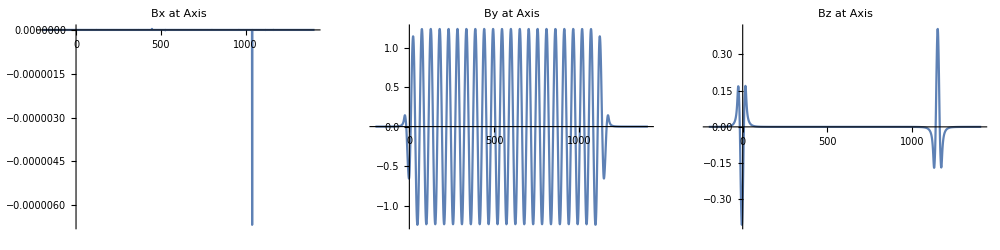

K parameter: 6.06078
Wavelenght: 1.4744×10^-8[m]

(1) RMS Phase Error [deg]: 2.09548

> Phase Error solved! (elapsed time: 25.81349[s])

(2-Fitting) RMS Phase Error [deg]: 0.437856

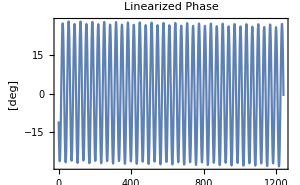
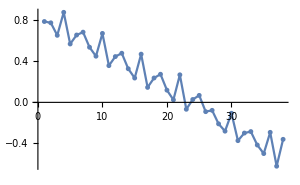

```mathematica
If[MemberQ[checkmode,3],

draw[mag,magn,ex,ey,checkgeo,espessurab,periodL,dist,layers,gap,3];
solve[undulator,magn];
If[MemberQ[check,1],field[undulator,xo,xf,nx]];
If[MemberQ[check,2],bforces[undulator,subdiv]];
If[MemberQ[check,3],cforces[cass1,cass2,cass3,cass4,subdivcass]];
If[MemberQ[check,4],interror2[undulator,xo,xf,nx]];
If[MemberQ[check,5],phaseerror[baxis,btotal,xo,xf,nx]];
If[MemberQ[check,6],mpError[undulator,gap,yo,yf,ney]];

save[isave,exportmatrix,expforces,exportfield,baxis];isave=isave+1;

]
```

## GV [lambda/4] (Pol. Elíptica)

Plot Undulator

> Undulator System Solved! (elapsed time: 39.6104358[s])

> Fields Calc. Solved! (elapsed time: 10.031239[s])

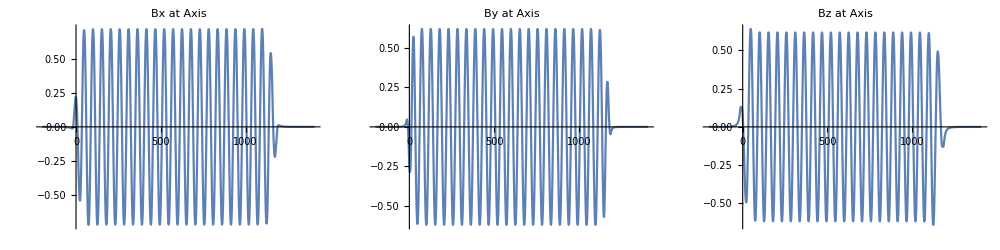

K parameter: 5.54344
Wavelenght: 1.24623×10^-8[m]

(1) RMS Phase Error [deg]: 2.69811

> Phase Error solved! (elapsed time: 25.57614[s])

(2-Fitting) RMS Phase Error [deg]: 0.445693

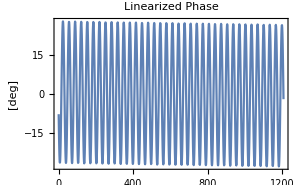
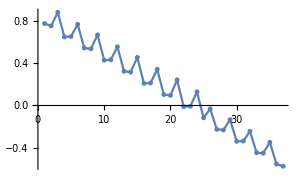

```mathematica
If[MemberQ[checkmode,4],

draw[mag,magn,ex,ey,checkgeo,espessurab,periodL,dist,layers,gap,4];
solve[undulator,magn];
If[MemberQ[check,1],field[undulator,xo,xf,nx]];
If[MemberQ[check,2],bforces[undulator,subdiv]];
If[MemberQ[check,3],cforces[cass1,cass2,cass3,cass4,subdivcass]];
If[MemberQ[check,4],interror2[undulator,xo,xf,nx]];
If[MemberQ[check,5],phaseerror[baxis,btotal,xo,xf,nx]];
If[MemberQ[check,6],mpError[undulator,gap,yo,yf,ney]];

save[isave,exportmatrix,expforces,exportfield,baxis];isave=isave+1;

]
```

## Export

```mathematica
If[Length[checkexp]==1,
exportf[exportmatrix,exportfield]
]
```

## Post - Calc

```mathematica
(*========= Physics Parameters =========*)
eletron=1.60217662*^-19; mo=9.10938356*^-31;
eRestEnergy=510998.92811; (*[eV]*) (* == mo*c^2[J]*)

bfield=baxis;
bfieldT=btotal;

(*Principal Longitudinal Axis*)
dx=(xf-xo)/nx;
longAxis=Table[xo+(n-1)*dx,{n,1,nx}];

(* Longitudinal Axis from 0 *)
s=(longAxis-longAxis[[1]])/1000;  (*[m]*)

(*========= Find Peaks =========*)
(*limits*)
ampX=0.1; ampY=0.1; ampZ=0.1;
(*Find Peaks*)
peakX=FindPeaks[bfield[[All,1]],0 ,0, ampX];
peakY=FindPeaks[bfield[[All,2]],0 ,0, ampY];
peakZ=FindPeaks[bfield[[All,3]],0 ,0, ampZ];
peakT=FindPeaks[bfieldT,0 ,0 , ampZ];

(* Remove extremities *)
peakT=Drop[peakT,{1,3}];peakT=Drop[peakT,{-3,-1}];
longPeakT=Table[s[[peakT[[i,1]]]],{i,1,Length[peakT]}];

If[Length[peakZ]>2,
peakZ=Drop[peakZ,{1,3}];peakZ=Drop[peakZ,{-3,-1}];
longPeakZ=Table[longAxis[[peakZ[[i,1]]]],{i,1,Length[peakZ]}];
,
peakZ=ConstantArray[10^-5,{1,2}];
];

If[Length[peakY]>2,
peakY=Drop[peakY,{1,3}];peakY=Drop[peakY,{-3,-1}];
longPeakY=Table[longAxis[[peakY[[i,1]]]],{i,1,Length[peakY]}];
,
peakY=ConstantArray[10^-5,{1,2}];
];

If[Length[peakX]>2,
peakX=Drop[peakX,{1,3}];peakX=Drop[peakX,{-3,-1}];
longPeakX=Table[longAxis[[peakX[[i,1]]]],{i,1,Length[peakX]}];
,
peakX=ConstantArray[10^-5,{1,2}];
];

If[Mean[peakX[[All,2]]]>Mean[peakY[[All,2]]],
If[Mean[peakX[[All,2]]]>Mean[peakZ[[All,2]]],
longPeak=longPeakX;Print["PeakX"]
,
longPeak=longPeakZ;Print["PeakZ"]
]
,
longPeak=longPeakY;Print["PeakY"]
];

periods=Table[longPeak[[i+1]]-longPeak[[i]],{i,1,Length[longPeak]-1}];
```

PeakX

```mathematica
(*========= Magnet design =========*)
nperiods=Length[periods];
periodL=Mean[periods]; (*mm*)
eEnergy=3*10^9; (*eV*)
gamma=eEnergy/eRestEnergy;
c=299792458; (*m/s*)
kparam=0.0934*periodL*Mean[peakT[[All,2]]];  (*!!!!!!!!!!!!! Todas componentes ou só 1? *)
lambda=((Mean[periods]/1000)/(2*(gamma^2)))*(1 + (kparam^2)/2); (*m*)
Print["\nK parameter: ",kparam,"\nWavelenght: ", lambda,"[m]"];

(*========= Integrals =========*)
intField0=Table[{(bfield[[i,1]]+bfield[[i+1,1]])/2*(longAxis[[i+1]]-longAxis[[i]])*10^-3,(bfield[[i,2]]+bfield[[i+1,2]])/2*(longAxis[[i+1]]-longAxis[[i]])*10^-3,(bfield[[i,3]]+bfield[[i+1,3]])/2*(longAxis[[i+1]]-longAxis[[i]])*10^-3},{i,1,Length[bfield]-1}]; (* [T.m] *)

intField={Accumulate[intField0[[All,1]]],Accumulate[intField0[[All,2]]],Accumulate[intField0[[All,3]]]};
```

K parameter: 5.54324
Wavelenght: 1.24614×10^-8[m]

```mathematica
(*========= Phase Function =========*)
I01[i_]:=(
Return[eletron/(gamma*mo*c)*intField[[1,i]]]
);

I02[i_]:=(
Return[eletron/(gamma*mo*c)*intField[[2,i]]]
);

I03[i_]:=(
Return[eletron/(gamma*mo*c)*intField[[3,i]]]
);

I2[j_]:=(
I0=Table[(((I01[i]^2+I01[i+1]^2)/2)+((I02[i]^2+I02[i+1]^2)/2)+((I03[i]^2+I03[i+1]^2)/2))*(s[[i+1]]-s[[i]]),{i,1,j}]; 
Return[Sum[I0[[i]],{i,1,Length[I0]}]];
);

(*========= Phase =========*)
phase=Table[Pi/lambda*(s[[j]]/gamma^2+I2[j]),{j,peakT[[1,1]],peakT[[Length[peakT],1]]-2}];
```

(1) RMS Phase Error [deg]: 2.70949

(2-Fitting) RMS Phase Error [deg]: 0.424088

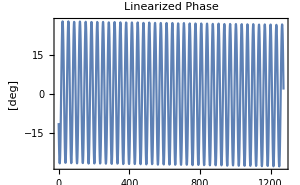
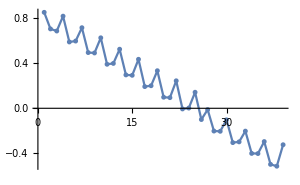

```mathematica
(*Phase Error*)
phaseError=Table[phase[[(peakT[[i+1,1]]-peakT[[1,1]]+1)]]-phase[[(peakT[[i,1]]-peakT[[1,1]]+1)]],{i,1,Length[peakT]-2}];
rmsError=RootMeanSquare[(phaseError-Pi)*180/Pi];
Print["(1) RMS Phase Error [deg]: ",rmsError];
(*Print[ListLinePlot[(phaseError-Pi)*180/Pi]];*)

(*========= Fitting ========= *)
fitData=Table[{s[[i]]+longPeakT[[1]],phase[[i]]},{i,1,Length[phase]}];
fitLin=NonlinearModelFit[fitData,a*x+b,{a,b},x];

linearFit=Table[{s[[i]]+longPeakT[[1]],fitLin[s[[i]]+longPeakT[[1]]]},{i,1,Length[phase]}];
linearizedPhase=phase-linearFit[[All,2]];

p3=ListLinePlot[linearizedPhase*180/Pi,PlotLabel->"Linearized Phase",ImageSize->{300,200},Frame->True,FrameLabel->{" ","[deg]"}];

errorP=Table[Mean[linearizedPhase[[peakT[[i,1]]-peakT[[1,1]]+1;;peakT[[i+1,1]]-peakT[[1,1]]-1]]],{i,1,Length[peakT]-1}]*180/Pi;
Print["(2-Fitting) RMS Phase Error [deg]: ",RootMeanSquare[errorP]];

Print[Row[{Show[p3],Show[ListLinePlot[errorP,ImageSize->{300,200},PlotMarkers->{Automatic, 5}]]}]]
```